# Add ReLU

```mathematica
relu[A_]:=MapThread[Max,{Array[0&,Dimensions@A],A},Length[Dimensions[A]]]
```

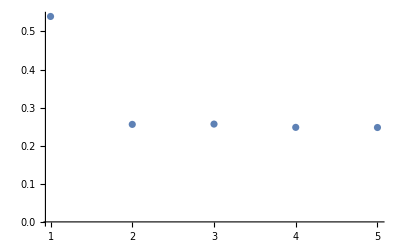

```mathematica
reluDot[A_,B_]:=relu[A.B];
errEq:=Y-Fold[reluDot,Reverse[vars]~Join~{makeW[0]}];
lossEq:=take1[1/(2 dsize)errEq.errEqᵀ];

gradEq=D[lossf[Wf],{Wf,1}];
gradf[Wf_]:=gradEq/.subW[Wf];
lossf[Wf_]:=(lossEq/.subW[Wf]/.subY/.subX);

optimizeRegular[lr_,w0f_,iters_]:=Module[{wf},
{pointList, gradList,preList, lossList}={{},{},{},{}};
wf=w0f;
For[iter=1,iter≤iters,iter++,
pointList=pointList~Append~wf;
gradList=gradList~Append~gradf[wf];
preList=preList~Append~ihessf[wf];
lossList=lossList~Append~lossf[wf];
wf=wf-lr*gradf[wf]
];
];
optimizeRegular[.5,W0f,5];
ListPlot[lossList,PlotRange->All]
```

```mathematica
Export["~/git/whitening/exp/data/natural_gradient_multilayer_losses_regular.csv",lossList];
```